# Homework 3 - Austin Hardaway

### 1.

```mathematica
(*(*given a f(x)= 0 and an interval [a0,b0] the claim is that the absolute error of the nth itteration is less than or equal to (b0-a0)/2^(n+1) so:*)
f1[x_]=0;
Cn = (a0+b0)/2;
(*because f(x)=0 for all x we don't have to consider the sign at f(c)*)
Cn+1 = (Cn+b0)/2 ;
(*and*)
Cn+1 = ((a0+b0)/2+b0)/2;
c1 =((a0+b0 + 2b0)/2)/2 = (a0+3b0)/2 *1/2 = (a0+3b0)/2^2≤ (a0 + b0)/2^(n+1); which is our result.
*)
```

### 2.

```mathematica
FindRoot[6(E^x-x)==6+3 x^2+2 x^3,{x,0}]
```

{x→0.}

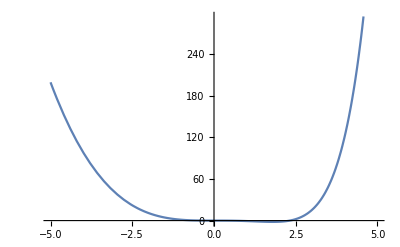

```mathematica
Plot[6(E^x-x) -6-3 x^2-2 x^3, {x,-5,5}]
```

```mathematica
(*so the Mathematica Root Finder works!*)
```

### 3.

```mathematica
nextInterval[f_,{a_,b_}]:= If[f[(a+b)/2]<0,{a,(a+b)/2},{(a+b)/2,b}];
```

```mathematica
f[x_]:= 6(E^x-x) -6-3 x^2-2 x^3;
 root= Nest[nextInterval[f,#]&,{0,1},15]
```

{0,1/32768}

```mathematica
N[f[root[[1]]],10]
```

0

```mathematica
(* so we approach the root around 0 with the initial conditions a=0 b=1*)
```

### 4.

```mathematica
(*challenge*)
```

### 5.

```mathematica
fn[x_]:= x^8-36 x^7-4536 x^5+22449 x^4-67284 x^3+118124 x^2-109584x+40320;
roots = NSolve[fn[t]== 0,t]
```

{{t→-3.80027-10.5793 ⅈ},{t→-3.80027+10.5793 ⅈ},{t→0.832536-2.1133 ⅈ},{t→0.832536+2.1133 ⅈ},{t→0.937354},{t→1.16233-0.595877 ⅈ},{t→1.16233+0.595877 ⅈ},{t→38.6735}}

```mathematica
(* weird interaction between 3 and 5 if I use x so change of variable to t*)
(* @TODO: Plot using list plot*)
```

### 6.

```mathematica
ftrig[x_]:=Tan[x]Tanh[x];
```

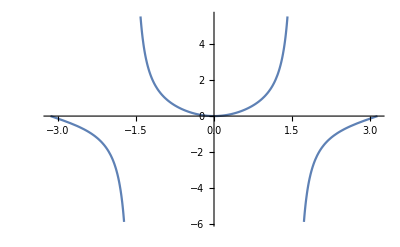

```mathematica
Plot[ftrig[t],{t,-π,π}]
```

```mathematica
falsePos[f_,{a_,b_}]:= b-(a-b)/(f[a]-f[b])f[b];
```

```mathematica
falsePos[ftrig,{.5,ftrig[.5]}]
```

0.168786

```mathematica
N[Nest[ftrig,{.5,ftrig[.5]},4],3]
```

{0.0000165418,2.73631×10^-10}

```mathematica
(*@Todo: table comparision between falsePos and biseciton*)
Table[{{i,ftrig[i]},falsePos[ftrig,{i,ftrig[i]}],nextInterval[ftrig,{i,i+1}]},{i,.1,2,.2}] //TableForm
```

0.1
0.0100002 | 0.00909105 | 0.6
1.1
0.3
0.0901136 | 0.0693265 | 0.8
1.3
0.5
0.252456 | 0.168786 | 1.
1.5
0.7
0.509052 | 0.306756 | 1.2
1.7
0.9
0.902649 | 0.535406 | 1.4
1.9
1.1
1.57279 | 1.10161 | 1.1
1.6
1.3
3.10402 | 3.08251 | 1.3
1.8
1.5
12.7639 | 12.9433 | 1.5
2.
1.7
-7.19947 | -5.83546 | 1.7
2.2
1.9
-2.799 | -3.4794 | 1.9
2.4

```mathematica
(*First itteration false position does better*)
```

### 7.

```mathematica
NewtonStep[{f_,xn_}] := {f,(xn-f[xn]/f'[xn])};
```

```mathematica
NewtonMethod[f_,t_, n_] :=N[Nest[NewtonStep, {f,t},n],5][[2]];
```

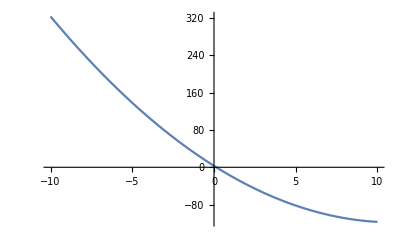

```mathematica
testFunc[t_]:= t^2-22t+3;
Plot[testFunc[t], {t,-10,10}]
```

```mathematica
FindRoot[testFunc[t],{t,1}]
```

{t→0.13722}

```mathematica
NewtonMethod[testFunc, 1, 5]
```

0.13722

### 8

```mathematica
steffG [t_,f_] := (f[t+f[t]]-f[t])/f[t];
SteffStep[{f_,xn_}] := {f,(xn-f[xn]/steffG[xn,f])};
```

```mathematica
SteffMethod[f_,xn_,n_] := N[Nest[SteffStep, {f,xn},n],5][[2]];
newTestFunc[t_]:=(t-1)^8;
```

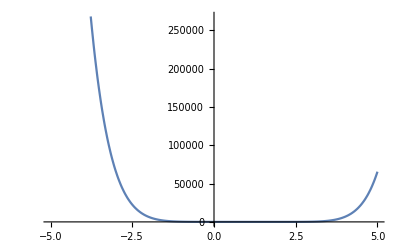

```mathematica
Plot[(t-1)^8, {t,-5,5}]
```

```mathematica
SteffMethod[newTestFunc, 1.2, 10]
```

1.05262

```mathematica
NewtonMethod[newTestFunc, 1.2, 10]
```

1.05262